## Apply Fourier Transform on a custom function

```mathematica
myf[x_,a_]:=Sin[x]*a^2+2 x^3+a/x Log[a*x];
```

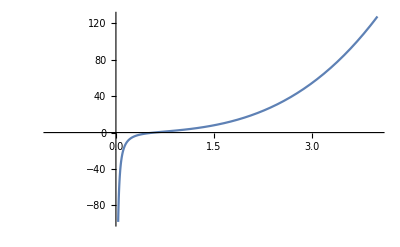

```mathematica
Plot[myf[x,1],{x,-1,4}]
```

```mathematica
FourierTransform[myf[x,1],x,ω]
```

ⅈ √(π/2) DiracDelta[-1+ω]-ⅈ √(π/2) DiracDelta[1+ω]-1/2 √(π/2) (2 ⅈ EulerGamma+π+2 ⅈ Log[Abs[ω]]) (-1+Sign[ω])+2 ⅈ √(2 π) DiracDelta^(3)[ω]

### Add test function from documentation

```mathematica
fDoc[t_]:=Exp[-t^2] Sin[t];
(*Apply Fourier Transform *)
ff[ω_]:=FourierTransform[fDoc[t],t,ω];
```

```mathematica
N[fDoc[1]]
```

0.30956

```mathematica
N[ff[1]]
```

0.+0.223488 ⅈ